1 - 6 RLC-Circuits: special cases

1. RC-Circuit. Model the RC-Circuit in the figure below. Find the current due to a constant E.

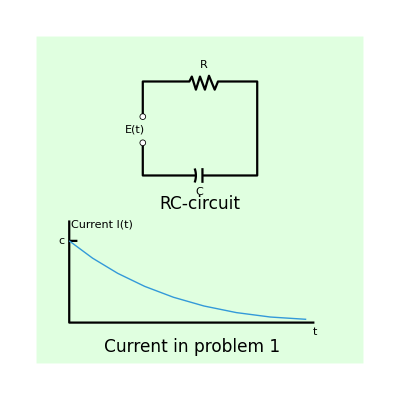

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,4}]},{Thickness[0.004],Line[{{1.3,2.7},{1.3,2.3},{1.95,2.3}}]},{Thickness[0.004],Circle[{1.7,2.3},0.25,{-0.35,0.35}]},{Thickness[0.004],Line[{{2.03,2.3},{2.7,2.3},{2.7,3.45},{2.22,3.45},{2.18,3.35},{2.11,3.52},{2.06,3.35},{2,3.51},{1.95,3.35},{1.9,3.51},{1.87,3.45},{1.3,3.45},{1.3,3.02}}]},{Thickness[0.004],Line[{{2.03,2.21},{2.03,2.39}}]},{Disk[{1.3,3.02},0.04]},{White,Disk[{1.3,3.02},0.03]},{Disk[{1.3,2.7},0.04]},{White,Disk[{1.3,2.7},0.03]},{Text[Style["E(t)",Medium],{1.2,2.86}]},{Text[Style["R",Medium],{2.05,3.65}]},{Text[Style["C",Medium],{1.99,2.1}]},{Text[Style["RC-circuit",17],{2,1.95}]},{Thickness[0.004],Line[{{0.4,1.75},{0.4,0.5},{3.4,0.5}}]},{Thickness[0.004],Line[{{0.4,1.5},{0.5,1.5}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,1.5},{1.5,0.6},{3.3,0.54}}]},{Text[Style["Current in problem 1",17],{1.9,0.2}]},{Text[Style["c",Medium],{0.3,1.5}]},{Text[Style["t",Medium],{3.4,0.38}]},{Text[Style["Current I(t)",Medium],{0.8,1.7}]}}]
```

```mathematica
ClearAll["Global`*"]
```

The problem is asking for a look at RC circuit, not RLC.

The site https : // www.intmath.com/differential - equations/6 - rc - circuits.php assumes a constant voltage source, just what the problem specifies. Below: There is no inductance here, only R and C.

```mathematica
eqnw=rR(D[eye[t],t])+eye[t]/cC==0
```

eye[t]/cC+rR eye'[t]==0

Within a certain range of capacitance and resistance, the plot resembles the one in the problem description, and can be manipulated to imitate changing parameters, with the voltage remaining constant.

```mathematica
sol2=DSolve[eqnw,eye,t]
```

{{eye→Function[{t},ⅇ^(-t/(cC rR)) C[1]]}}

It looks like the current is normalized to 1 at t=0, and the fraction of its max value at a given time needs to be estimated from the underlying grid.

```mathematica
Manipulate[Plot[ⅇ^(-t/(cC rR)),{t,0,3},PlotRange->All,GridLines->All
],{rR,0.2,10},{cC,0.01,1} ]
```

A random scrap from a different perspective, kept as interesing junk.

```mathematica
{ind, cap, res}={l i'[t]==Subscript[v, l][t],Subscript[v, c]'[t]==1/c i[t],r i[t]==Subscript[v, r][t]};
kirchhoff=Subscript[v, l][t]+Subscript[v, c][t]+Subscript[v, r][t]==Subscript[v, s][t];
```

3. RL-Circuit. Model the RL-circuit in the figure below. Find a general solution when R, L, E are any constants. Graph or sketch solutions when L = 0.25 H, R = 10 Ω, and E = 48 V.

The above screenshot came from the online app at https://falstad.com/circuit/. The current it shows agrees with the old formula for current, I=E/R, and was captured after the resistance had plenty of time to decay. And that’s all it is, except that there is a time constant to apply. The time constant becomes ever smaller as the operation time increases. Since the problem description talks in terms of a constant state, it seems the time constant would become vanishingly small, leaving merely I=E/R=4.8 amps.

```mathematica
ClearAll["Global`*"]
```

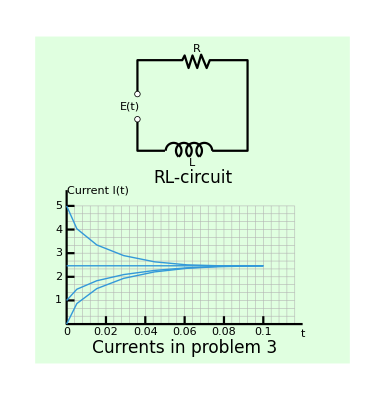

```mathematica
rangex=Range[0.4,3.3,0.1];
rangey=Range[0.5,2,0.1];
Graphics[{{LightGreen,Rectangle[{0,0},{4,4.15}]},{RGBColor[0.7,0.7,0.7],Thickness[0.001],Line[Table[{{0.4,j},{3.3,j}},{j,0.5,2,0.1}]]},{RGBColor[0.7,0.7,0.7],Thickness[0.001],Line[Table[{{j,0.5},{j,2}},{j,0.4,3.3,0.1}]]},{Thickness[0.004],Line[{{1.3,3.1},{1.3,2.7},{1.65,2.7}}]},{Thickness[0.004],Circle[{1.76,2.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,2.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,2.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,2.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,2.7},{2.7,2.7},{2.7,3.85},{2.22,3.85},{2.18,3.75},{2.11,3.92},{2.06,3.75},{2,3.91},{1.95,3.75},{1.9,3.91},{1.87,3.85},{1.3,3.85},{1.3,3.42}}]},{Disk[{1.3,3.42},0.04]},{White,Disk[{1.3,3.42},0.03]},{Disk[{1.3,3.1},0.04]},{White,Disk[{1.3,3.1},0.03]},{Text[Style["E(t)",Medium],{1.2,3.26}]},{Text[Style["R",Medium],{2.05,3.99}]},{Text[Style["L",Medium],{1.99,2.54}]},{Text[Style["RL-circuit",17],{2,2.35}]},{Thickness[0.004],Line[{{0.4,2.2},{0.4,0.5},{3.4,0.5}}]},{Thickness[0.004],Line[{{0.4,0.8},{0.5,0.8}}]},{Thickness[0.004],Line[{{0.4,1.1},{0.5,1.1}}]},{Thickness[0.004],Line[{{0.4,1.4},{0.5,1.4}}]},{Thickness[0.004],Line[{{0.4,1.7},{0.5,1.7}}]},{Thickness[0.004],Line[{{0.4,2},{0.5,2}}]},{Thickness[0.004],Line[{{0.9,0.5},{0.9,0.6}}]},{Thickness[0.004],Line[{{1.4,0.5},{1.4,0.6}}]},{Thickness[0.004],Line[{{1.9,0.5},{1.9,0.6}}]},{Thickness[0.004],Line[{{2.4,0.5},{2.4,0.6}}]},{Thickness[0.004],Line[{{2.9,0.5},{2.9,0.6}}]},{Text[Style["0.02",Medium],{0.9,0.4}]},{Text[Style["0.04",Medium],{1.4,0.4}]},{Text[Style["0.06",Medium],{1.9,0.4}]},{Text[Style["0.08",Medium],{2.4,0.4}]},{Text[Style["0.1",Medium],{2.9,0.4}]},{Text[Style["0",Medium],{0.4,0.4}]},{RGBColor[0.2,0.6,0.85],Line[{{0.4,1.24},{2.9,1.24}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,2},{0.55,1.1},{2.4,1.26},{2.9,1.24}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,0.5},{0.55,1.3},{2.4,1.22},{2.9,1.24}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,0.8},{0.55,1.23},{2.4,1.24},{2.9,1.24}}]},{Text[Style["Currents in problem 3",17],{1.9,0.2}]},{Text[Style["5",Medium],{0.3,2}]},{Text[Style["4",Medium],{0.3,1.7}]},{Text[Style["3",Medium],{0.3,1.4}]},{Text[Style["2",Medium],{0.3,1.1}]},{Text[Style["1",Medium],{0.3,0.8}]},{Text[Style["t",Medium],{3.4,0.38}]},{Text[Style["Current I(t)",Medium],{0.8,2.2}]}}]
```

When there are a lot of variables to watch, the Manipulate command is the only way I know to get an overview. The box below is based on the material at https://www.electronics-tutorials.ws/inductor/lr-circuits.html and may not agree with the text in detail.

```mathematica
eye[vee_,are_,ell_,tee_]=vee/are(1-ⅇ^(-(are tee)/ell))
```

((1-ⅇ^(-(are tee)/ell)) vee)/are

It takes some time for the current to reach its max value. From t=0.4 on in the green grid below, the circuit current is nominal.

```mathematica
Grid[Table[{tee,eye[48,10,0.25,tee]},{tee,0,0.6,0.1}],Frame->All]
```

0. | 0.
0.1 | 4.71208
0.2 | 4.79839
0.3 | 4.79997
0.4 | 4.8
0.5 | 4.8
0.6 | 4.8

```mathematica
veel[vee_,are_,ell_,tee_]=vee(ⅇ^(-(are tee)/ell))
```

ⅇ^(-(are tee)/ell) vee

```mathematica
Manipulate[Plot[{Abs[eye[vee,are,ell,tee]],Abs[veel[vee,are,ell,tee]],Abs[eye[48,10,0.25,tee]]},{tee,0,5},
PlotLegends->{"I=V/R(1-ⅇ^(-FractionBox[R t, L]))","V_L=V(ⅇ^(-FractionBox[R t, L]))","L=0.25H,R=10Ω,E=48V"},
PlotRange->{{0,0.1},{0,10}},AxesLabel->{"time","current I"},AspectRatio->0.5],{are,1,200},{ell,0.01,10} ,{vee,1,50}]
```

5.  LC-Circuit. This is an RLC-circuit with negligibly small R (analog of an undamped mass-spring system). Find the current when L=0.5 H, C = 0.005 F, and E = Sin[t] V, assuming zero initial current and charge.

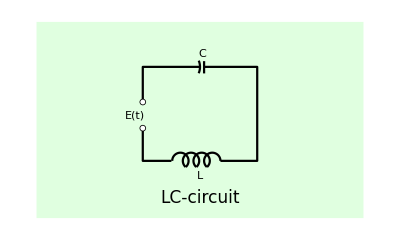

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,2.4}]},{Thickness[0.004],Line[{{1.3,1.1},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.85},{2.05,1.85}}]},{Thickness[0.004],Line[{{2,1.85},{1.3,1.85},{1.3,1.42}}]},{Thickness[0.004],Line[{{2.05,1.77},{2.05,1.92}}]},{Thickness[0.004],Circle[{1.8,1.85},0.2,{-0.4,0.39}]},{Disk[{1.3,1.42},0.04]},{White,Disk[{1.3,1.42},0.03]},{Disk[{1.3,1.1},0.04]},{White,Disk[{1.3,1.1},0.03]},{Text[Style["E(t)",Medium],{1.2,1.26}]},{Text[Style["C",Medium],{2.025,2.01}]},{Text[Style["L",Medium],{2.0,0.51}]},{Text[Style["LC-circuit",17],{2,0.25}]}}]
```

I ran across a couple of snippets, including one from the Mathematica documentation, suggesting that state space modeling would be a good way to look at circuits in Mathematica. I use it here.

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqns={eL q''[t]+aR q'[t]+1/cC q[t]==Vee[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{Vee[t],0}},{q'[t]},t]
```

010-1/(cC eL)-aR/eL1/eL010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

Here I put in the given parameters, taking the opportunity to equate the resistance with zero.

```mathematica
ms=m1/.{cC->0.005,eL->0.5,aR->0}
```

010-400.0.2.010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

The way to get output from a state space model is to use the command OutputResponse. Since the voltage depends on a periodic function, I drop the V for the input field, the voltage, because it is just a label.

```mathematica
outz=OutputResponse[{ms},Sin[t ],t]
```

{(1.46082×10^-17+0.0526316 ⅈ) ((0.+0.0952381 ⅈ) Cos[20. t]-(0.+1. ⅈ) Cos[19. t] Cos[20. t]+(0.+0.904762 ⅈ) Cos[20. t] Cos[21. t]-(1.66533×10^-16-7.21645×10^-17 ⅈ) Cos[20. t] Sin[19. t]-(2.24688×10^-17+6.60847×10^-19 ⅈ) Sin[20. t]+(2.35922×10^-16+6.93889×10^-18 ⅈ) Cos[19. t] Sin[20. t]-(2.13454×10^-16+6.27805×10^-18 ⅈ) Cos[21. t] Sin[20. t]+(5.96745×10^-17-1. ⅈ) Sin[19. t] Sin[20. t]+(1.50673×10^-16-6.52917×10^-17 ⅈ) Cos[20. t] Sin[21. t]-(5.39912×10^-17-0.904762 ⅈ) Sin[20. t] Sin[21. t])}

It is necessary to clean up the result with a small Chop.

```mathematica
outt=Chop[ComplexExpand[Re[outz]],10^-16]//FullSimplify
```

{0.00501253 Cos[1. t]-0.00501253 Cos[20. t]+3.46945×10^-18 Cos[39. t]}

Recognizing the periodic value of cosine, I can get the expression ready for a second chop by doing

```mathematica
outtf=outt/.Cos[39.t]->1
```

{3.46945×10^-18+0.00501253 Cos[1. t]-0.00501253 Cos[20. t]}

And then the Chop.

```mathematica
outtff=Chop[%,10^-17]
```

{0.00501253 Cos[1. t]-0.00501253 Cos[20. t]}

Testing the identity of those coefficients

```mathematica
1/0.005012531328320802
```

199.5

I find that the answer matches the text answer, justifying the green coloration above.

The plot is interesting.

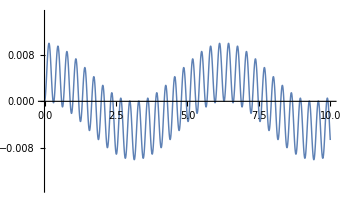

```mathematica
Plot[outtff,{t,0,10},ImageSize->350,AspectRatio->0.6,PlotRange->{{-0.01,10},{-0.015,0.015}},PlotStyle->Thickness[0.003]]
```

7 - 18 General RLC-circuits

7.  Tuning. In tuning a sterio system to a radio station, we adjust the tuning control (turn a knob) that changes C (or perhaps L) in an RLC-circuit so that the amplitude of the steady-state current, numbered line (5), p. 95 becomes maximum. For what C will this happen?

It is where the particular solution of the homogeneous equation is maximized. Numbered line (5) looks like

I_p(t)=I_0 Sin[ω t-θ]

The quantity θ is known as the phase lag, and, I suppose, the signal is best, I_p maximized, when θ equals zero.

8 - 14 Find the steady-state current in the RLC-circuit in the figure below for the given data.

9.  R = 4 Ω, L = 0.1 H, C = 0.05 F, E = 110 V

L D[q[t],{t,2}]+R D[q[t],t]-1/C q[t]=v[t]

```mathematica
eqn=0.1q''[t]+4q'[t]-1/0.05 q[t]==110
```

-20. q[t]+4 q'[t]+0.1 q''[t]==110

```mathematica
sol=DSolve[eqn,q,t]
```

{{q→Function[{t},-5.5+ⅇ^(-44.4949 t) C[1]+ⅇ^(4.4949 t) C[2]]}}

If C[1]=C[2]=0, then the green cell above matches the text answer.

11.  R = 12 Ω, L = 0.4 H, C = 1/80F, E = 220 Sin[10 t] V

The state space method has been working where former methods I tried did not, so it makes sense to stick with it.

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqns={eL q''[t]+aR q'[t]+1/cC q[t]==Vee[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{Vee[t],0}},{q'[t]},t]
```

010-1/(cC eL)-aR/eL1/eL010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

Here I put in the given parameters.

```mathematica
ms=m1/.{cC->1/80,eL->0.4,aR->12}
```

010-200.-30.2.5010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

The way to get output from a state space model is to use the command OutputResponse.

```mathematica
outz=OutputResponse[{ms},220Sin[10t ],t]
```

{0.+ⅇ^(-30. t) (22. ⅇ^(10. t)-27.5 ⅇ^(20. t)-7.10543×10^-15 ⅇ^(20. t) Cos[10. t]+5.5 ⅇ^(30. t) Cos[10. t]+7.10543×10^-15 ⅇ^(20. t) Sin[10. t]+16.5 ⅇ^(30. t) Sin[10. t]+7.10543×10^-15 ⅇ^(40. t) Sin[10. t])}

It is necessary to clean up the result with a Chop.

```mathematica
outt=Chop[outz,10^-14]//FullSimplify
```

{22. ⅇ^(-20. t)-27.5 ⅇ^(-10. t)+5.5 Cos[10. t]+16.5 Sin[10. t]}

I guess the ⅇ factors can be dropped if they are small enough, say, at 3 seconds.

```mathematica
N[-27.500000000000007 ⅇ^(-10. t)]/.t->3
```

-2.57335×10^-12

Evidently the text considers that size to be negligible, leaving

```mathematica
5.5 Cos[10. t]+16.5 Sin[10. t]
```

as the answer. The plot looks routine.

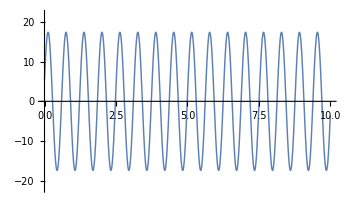

```mathematica
Plot[5.5 Cos[10. t]+16.5 Sin[10. t],{t,0,10},ImageSize->350,AspectRatio->0.6,PlotRange->{{-0.01,10},{-22,22}},PlotStyle->Thickness[0.003]]
```

13.  R = 12, L = 1.2 H, C = 20/3*10^-3 F, E = 12,000 Sin[25 t] V

C=20/3*1/1000=20/3000=2/300

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqns={eL q''[t]+aR q'[t]+1/cC q[t]==Vee[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{Vee[t],0}},{q'[t]},t]
```

010-1/(cC eL)-aR/eL1/eL010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

Here I put in the given parameters.

```mathematica
ms=m1/.{cC->20/3*10^-3,eL->1.2,aR->12}
```

010-125.-10.0.833333010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

The way to get output from a state space model is to use the command OutputResponse.

```mathematica
outz=OutputResponse[{ms},12000Sin[25t ],t]
```

{(0.+0. ⅈ)-(400.+1.56319×10^-14 ⅈ) ⅇ^(-5. t) ((-1.+0. ⅈ) Cos[10. t]+(1.+0. ⅈ) ⅇ^(5. t) Cos[10. t]^2 Cos[25. t]+(0.75-4.80505×10^-16 ⅈ) Sin[10. t]-(3.19744×10^-16-3.21521×10^-16 ⅈ) ⅇ^(5. t) Cos[10. t] Cos[25. t] Sin[10. t]+(1.+2.45581×10^-16 ⅈ) ⅇ^(5. t) Cos[25. t] Sin[10. t]^2-(0.5-7.49623×10^-17 ⅈ) ⅇ^(5. t) Cos[10. t]^2 Sin[25. t]+(1.42109×10^-16-9.97247×10^-17 ⅈ) ⅇ^(5. t) Cos[10. t] Sin[10. t] Sin[25. t]-(0.5-1.39035×10^-16 ⅈ) ⅇ^(5. t) Sin[10. t]^2 Sin[25. t])}

It is necessary to clean up the result with a Chop.

```mathematica
outt=Chop[ComplexExpand[Re[outz]], 10^-15]//Simplify
```

{-300. ⅇ^(-5. t) Sin[10. t]+Cos[10. t] (400. ⅇ^(-5. t)+1.27898×10^-13 Cos[25. t] Sin[10. t])-2.84217×10^-14 Sin[20. t] Sin[25. t]+Cos[10. t]^2 (-400. Cos[25. t]+200. Sin[25. t])+Sin[10. t]^2 (-400. Cos[25. t]+200. Sin[25. t])}

There is a sin^2+cos^2 trig identity in the above, but I’m going to have to pull it out by hand.

```mathematica
outhnd=-300. ⅇ^(-5. t) Sin[10. t]+Cos[10. t] (400. ⅇ^(-5. t))+ (-400. Cos[25. t]+200. Sin[25. t])
```

400. ⅇ^(-5. t) Cos[10. t]-400. Cos[25. t]-300. ⅇ^(-5. t) Sin[10. t]+200. Sin[25. t]

```mathematica
outhnd2=Collect[outhnd,ⅇ^(-5.t)]
```

```mathematica
Clear["Global`*"]
```

-400. Cos[25. t]+ⅇ^(-5. t) (400. Cos[10. t]-300. Sin[10. t])+200. Sin[25. t]

While I was pulling things out by hand, I pulled out a choppable term. The text constant B is equal to -300. The text constant A is equal to 1 in one position and 400 in another position. That makes my answer wrong, technically. I guess I should make it yellow, though I don’t feel it is a just action to do so. I feel like it is correct.

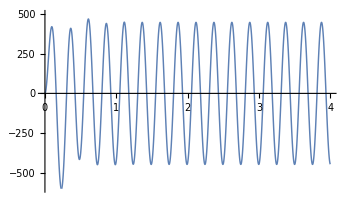

```mathematica
Plot[-400. Cos[25. t]+ⅇ^(-5. t) (400. Cos[10. t]-300. Sin[10. t])+200. Sin[25. t],{t,0,4},ImageSize->350,AspectRatio->0.6,PlotRange->{{-0.01,4},{-600,500}},PlotStyle->Thickness[0.003]]
```

15. Cases of damping. What are the conditions for an RLC-circuit to be (I) overdamped, (II) critically damped, (III) underdamped? What is the critical resistance R_crit (the analog of the critical damping constant 2 √(m k) ?

16 - 18 Solve the initial value problem for the RLC-circuit shown below, with the given data, assuming zero initial current and charge. Graph or sketch the solution.

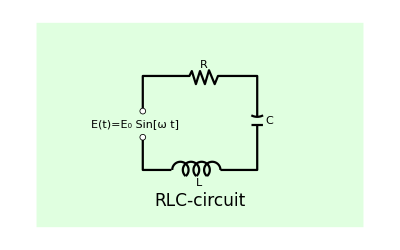

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,2.5}]},{Thickness[0.004],Line[{{1.3,1.1},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.25}}]},{Thickness[0.004],Line[{{2.63,1.25},{2.77,1.25}}]},{Thickness[0.004],Circle[{2.7,1.5},0.15,{-π/2-0.5,-π/2+0.5}]},{Thickness[0.004],Line[{{2.7,1.35},{2.7,1.85},{2.22,1.85},{2.18,1.75},{2.11,1.92},{2.06,1.75},{2,1.91},{1.95,1.75},{1.9,1.91},{1.87,1.85},{1.3,1.85},{1.3,1.42}}]},{Disk[{1.3,1.42},0.04]},{White,Disk[{1.3,1.42},0.03]},{Disk[{1.3,1.1},0.04]},{White,Disk[{1.3,1.1},0.03]},{Text[Style["E(t)=E_0 Sin[ω t]",Medium],{1.2,1.26}]},{Text[Style["R",Medium],{2.05,1.99}]},{Text[Style["L",Medium],{1.99,0.54}]},{Text[Style["RLC-circuit",17],{2,0.32}]},{Text[Style["C",Medium],{2.85,1.3}]}},Axes->False]
```

17.  R = 6 Ω, L = 1 H, C = 0.04 F, E = 600(Cos[t] + 4 Sin[t])V

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqns={eL q''[t]+aR q'[t]+1/cC q[t]==Vee[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{Vee[t],0}},{q'[t]},t]
```

010-1/(cC eL)-aR/eL1/eL010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

Here I put in the given parameters.

```mathematica
ms=m1/.{cC->0.04,eL->1,aR->6}
```

010-25.-61010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{Vee[t],0}},Automatic,t

The way to get output from a state space model is to use the command OutputResponse.

```mathematica
outz=OutputResponse[{ms},600(Cos[t]+4Sin[t]),t]
```

{(0.+0. ⅈ)+ⅇ^(-3. t) ((-100.-1.11022×10^-14 ⅈ) Cos[4. t]+(100.+1.11022×10^-14 ⅈ) ⅇ^(3. t) Cos[t] Cos[4. t]^2-(1.87214×10^-14-1.65445×10^-14 ⅈ) ⅇ^(3. t) Cos[4. t]^2 Sin[t]+(75.+1.52656×10^-14 ⅈ) Sin[4. t]-(8.65974×10^-15+1.80411×10^-14 ⅈ) ⅇ^(3. t) Cos[t] Cos[4. t] Sin[4. t]+(2.27374×10^-13+2.91161×10^-14 ⅈ) ⅇ^(3. t) Cos[4. t] Sin[t] Sin[4. t]+(100.-1.14492×10^-14 ⅈ) ⅇ^(3. t) Cos[t] Sin[4. t]^2-(0.+7.91555×10^-14 ⅈ) ⅇ^(3. t) Sin[t] Sin[4. t]^2)}

```mathematica
outt=Chop[ComplexExpand[Re[outz]]]//Simplify
```

{-100. ⅇ^(-3. t) Cos[4. t]+100. Cos[t] Cos[4. t]^2+Sin[4. t] (75. ⅇ^(-3. t)+100. Cos[t] Sin[4. t])}

```mathematica
outtf=Collect[outt,ⅇ^(-3.t)]
```

{100. Cos[t] Cos[4. t]^2+100. Cos[t] Sin[4. t]^2+ⅇ^(-3. t) (-100. Cos[4. t]+75. Sin[4. t])}

I can see the sin^2+cos^2 identity in the above, but will have to take it out by hand.

```mathematica
100. Cos[t]+ⅇ^(-3. t) (-100. Cos[4. t]+75. Sin[4. t])
```

And with that, the above cell matches the text answer.

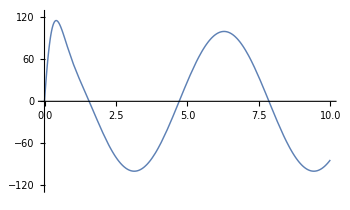

```mathematica
Plot[100. Cos[t]+ⅇ^(-3. t) (-100. Cos[4. t]+75. Sin[4. t]),{t,0,10},ImageSize->350,AspectRatio->0.6,PlotRange->{{-0.01,10},{-125,125}},PlotStyle->Thickness[0.003]]
```

19. Writing report. Mechanical-electrical analogy. Explain table 2.2 (reproduced below) in a 1 - 2 page report with examples, e.g. the analog (with L = 1 H) of a mass-spring system of mass 5 kg, damping constant 10 kg/sec, spring constant 60 kg/sec^2, and driving force 220 cos 10t kg/sec.

```mathematica
Grid[{{Item[Electrical System,Background->RGBColor[1,0.8,0.5]], Item[Mechanical System,Background->RGBColor[1,0.8,0.5]]},{Inductance L, "Mass m"},{"Reciprocal 1/c of capacitance","Spring modulus k"},{"Derivative E_0ω Cos[ω t] of electromotive force","Driving force F_0Cos[ω t]"},{"Current I(t)","Displacement y(t)"}}, Frame->All]
```

Electrical System | Mechanical System
Inductance L | Mass m
Reciprocal 1/c of capacitance | Spring modulus k
Derivative E_0ω Cos[ω t] of electromotive force | Driving force F_0Cos[ω t]
Current I(t) | Displacement y(t)

The equivalent equations of state are given on p. 97 as

```mathematica
Subscript[L, e]*Subscript[I, e]''[t] + Subscript[R, e]*Subscript[I, e]'[t]+1/Subscript[C, e]*Subscript[I, e][t]=Subscript[E, 0]*ω*Cos[ω t]
```

for the electrical version and

```mathematica
m*y''[t]+c*y'[t]+k*y[t]=Subscript[F, 0] Cos[ω t]
```

for the mechanical version. The problem details of the mechanical system are set forth as

```mathematica
m=5;
c=10;
k=60;
Subscript[F, 0]=220 Cos[10 t];
```

To see if I have the mechanical side down, let me try to get a function for the displacement y.

```mathematica
eqn1=5y''[t]+10y'[t]+60 y[t]==220Cos[10 t]
```

60 y[t]+10 y'[t]+5 y''[t]==220 Cos[10 t]

Mathematica solves the equation without difficulty; however, the solution is not as simple an expression as I could wish.

```mathematica
sol=DSolve[eqn1,y,t];
```

The solution does backtest successfully.

```mathematica
eqn1/.sol//Simplify
```

{True}

And the resulting plot is typical of a forced SHM.

```mathematica
solp=sol/.{C[1]->1,C[2]->1};
```

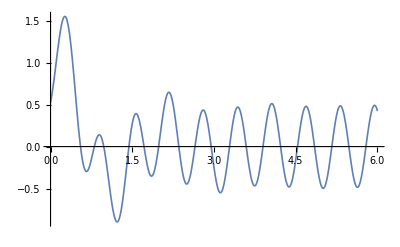

```mathematica
Plot[y[t]/.solp,{t,0,6},PlotStyle->Thickness[0.003]]
```

I can extract the actual function

```mathematica
solpt=solp[[1,1,2,2]];
```

and make a table of a few of its output points.

```mathematica
Table[{n,solpt/.t->n},{n,0,2,0.1}]
```

{{0.,0.524558},{0.1,0.984198},{0.2,1.44535},{0.3,1.51068},{0.4,1.04147},{0.5,0.312714},{0.6,-0.208772},{0.7,-0.263182},{0.8,-0.00994748},{0.9,0.13955},{1.,-0.0861754},{1.1,-0.562744},{1.2,-0.884539},{1.3,-0.743297},{1.4,-0.221009},{1.5,0.273882},{1.6,0.369945},{1.7,0.0631134},{1.8,-0.288775},{1.9,-0.301581},{2.,0.0781706}}

The lhs variables are easily determined when the proportionality constant resultant from a mechanical system based on 5 kg and an electrical one based on 1 H is considered. That would be

```mathematica
1 H, 2Ω, and 1/12 Farad
```

To solve the rhs I can first solve the coefficient situation,

```mathematica
Solve[5*10*x*Cos[10 t]-220*Cos[ 10 t]==0,x]
```

{{x→22/5}}

and then consider that because what is wanted is the derivative of the electromotive force, I will be looking at

```mathematica
-4.4Sin[10 t]
```

as the rhs. The text answer agrees, except it does not show a negative sign, and in terms of making up the system equation I believe the voltage expression on the rhs is better left unsigned.